## Functions

```mathematica
<<HypothesisTesting`
```

```mathematica
TwoBenfordsLawProb[d_]:=Module[{},
N[∑_(k=1)^9 Log[10,1+(10k+d)^-1]]
]
twoBLProbs=Map[TwoBenfordsLawProb,Range[0,9]]
```

{0.119679,0.11389,0.108821,0.10433,0.100308,0.0966772,0.0933747,0.090352,0.0875701,0.0849974}

```mathematica
GetSignificantDigit[num_,dig_]:=Module[{digits},
digits=RealDigits[num];
If[digits[[2]]≠  1,
Return[digits[[1,dig]]],
Return[digits[[1,1]]]]
];
```

```mathematica
DigitProbs[data_,digitPos_]:=Module[{},
Transpose[MapAt[N[#/Length[data]]&,Transpose[Sort[Tally[Map[GetSignificantDigit[#,digitPos]&,data]]]]
,2]]]
```

```mathematica
DigitTally[data_,digitPos_]:=Module[{tally,size,range,freeq,posq,missing},
tally=Sort[Tally[Map[GetSignificantDigit[#,digitPos]&,data]]];
range=If[digitPos==1,Range[9],Range[0,9]];
If[Length[range]==Length[tally],tally,
freeq=Map[FreeQ[tally[[All,1]],#]&,range];
missing=Map[{#,0}&,Pick[range,freeq,True]];
Sort[Join[tally,missing]]
]
]
```

```mathematica
X2B2[list_]:=Module[{tallySecondDigit,totalSecondDigit,x2B2},
tallySecondDigit=DigitTally[list,2];
totalSecondDigit=Total[tallySecondDigit[[All,2]]];
x2B2=∑_(i=1)^10 (tallySecondDigit[[i,2]]-totalSecondDigit*twoBLProbs[[i]])^2/(totalSecondDigit*twoBLProbs[[i]])
]
```

```mathematica
St[alpha_,T_]:=Module[{},
Map[(#*alpha)/T&,Range[T]]
]
```

```mathematica
PValue[stat_]:=Module[{df,pvalue},
df=9;
pvalue=Last[ChiSquarePValue[stat,9,TwoSided-> False]];
If[stat<9,
1-pvalue,
pvalue
]
]
```

```mathematica
PValueMap[stats_]:=Module[{},
Map[PValue[#]&,stats]
]
```

```mathematica
Stats[data_]:=Module[{},
{"Mean:"<>ToString[N[Mean[data]]],"Median:"<>ToString[N[Median[data]]],"Min:"<>ToString[Min[data]],"Max:"<>ToString[Max[data]],"Skewness:"<>ToString[N[Skewness[data]]]}
]
```

```mathematica
BLHistogram[data_]:=Module[{},BarChart[Transpose[{twoBLProbs,DigitProbs[data,2][[All,2]]}],ChartLegends-> {"2BL","Data"},ChartStyle->{Green,Blue},ChartLabels-> {Range[0,9],None},PlotLabel-> "Second Digit Benford Expected Frequency",ImageSize-> Medium]]
```

```mathematica
DistrictVoteGenerator[cand_,weights_,numVotes_]:=Module[{votes,missing,tally,i},
votes=RandomChoice[weights->cand ,numVotes];
tally=Tally[votes];
missing=Flatten[Position[Map[MemberQ[votes,#]&,cand],False]];
For[i=1,i≤ Length[missing],i++,
tally=Append[tally,{cand[[missing[[i]]]],0}];];
Flatten[Map[Cases[tally,{#,_}][[All,2]]&,cand]]
]
```

```mathematica
DataLogPlot[data_]:=Module[{log10},
log10=Map[N[Log[10,#]]&,data];
Histogram[log10,Automatic,"Probability"]
]
```

```mathematica
MechA[size_,mf_,lgp_,hgp_,lb_,ha_]:=Module[{lgb,hgb,mgb,p3,q,pf,votes},
lgb=Exp[lgp]/(Exp[lgp]+Exp[hgp]+1);
hgb=Exp[hgp]/(Exp[lgp]+Exp[hgp]+1);
mgb=1/(Exp[lgp]+Exp[hgp]+1);
p3={RandomVariate[BetaDistribution[1/2,lb]],mf,RandomVariate[BetaDistribution[ha,1/2]]};
q=RandomVariate[UniformDistribution[{0,1}]];
pf={q*lgb,mgb,(1-q)*hgb};
votes=Round[Total[size*p3*pf/Total[pf]]];
{votes,size-votes}]
```

```mathematica
AdjustedPValue[p_]:=Module[{adjusted,T,pSorted,j},
pSorted=Sort[p];
T=Length[p];

adjusted={};

For[j=1,j≤T,j++,
adjusted=Append[adjusted,Min[Map[Min[T/#*pSorted[[#]],1]&,Range[j,T]]]]
];

adjusted
]
```

## Random Counts

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
```

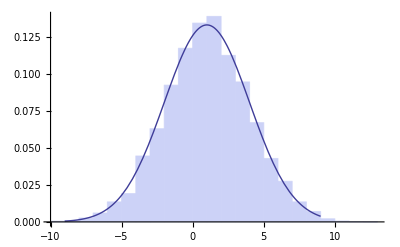

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick]]
```

## Controlled FDR

#### Functions

```mathematica
ControlledFDR[sectionPvalues_,print_,countyIDs_]:=Module[{dim,T,alpha,newAlpha,stVals,sts,stData,stDataSorted,d,i,desicion,x2b2TableExtended,rejecitonPositions,labels},
dim=Dimensions[sectionPvalues];
T=dim[[1]]*dim[[2]];
alpha=0.05;
newAlpha=alpha/T;
stVals=St[alpha,T];
stData=Transpose[{Flatten[sectionPvalues],Range[T]}];stDataSorted=SortBy[stData,First];

d=0;
For[i=0,i≤ T-1,i++,
If[stDataSorted[[i+1,1]]<stVals[[i+1]],
d=i+1;
];
];

desicion=ReplacePart[Table["Accepted",{i,T}],Partition[Range[d],1]->"Rejected"];
labels={"d","PValue","ID","St","Decision"};
x2b2TableExtended=Prepend[Transpose[Join[{Range[T]},Transpose[stDataSorted],{stVals},{desicion}]],labels];

rejecitonPositions=Map[Coord[#,dim[[2]]]&,Pick[stDataSorted[[All,2]],desicion,"Rejected"]];

If[print,
Print["d = ",d];
Print[TableForm[x2b2TableExtended]];
];
rejecitonPositions
];
```

```mathematica
StolenVotes[precinct_,stolenPer_,favCand_]:=Module[{stolen,n1,n2,lossers,losserCounts,winnerCount,nCands,outCounts,counts,tvotes},
tvotes=precinct[[1]];
counts=precinct[[3;;]];
nCands=Length[counts];
stolen=Round[tvotes*stolenPer];
n1=RandomInteger[{stolen}];
n2=stolen-n1;
lossers=Complement[Range[nCands],{favCand}];
losserCounts=MapThread[If[counts[[#1]]-#2<0,0,counts[[#1]]-#2]&,{lossers,{n1,n2}}];
winnerCount=counts[[favCand]]+stolen;
outCounts=Table[0,{x,nCands}];
outCounts[[favCand]]=winnerCount;
outCounts[[lossers]]=losserCounts;
Join[precinct[[;;2]],outCounts]
]
```

#### Work

```mathematica
rawStateData=Import[nd<>"states//Alaska1.txt","Table"];
(*Serial N, Population, County ID, Candidate Votes*)
delData=rawStateData[[2;;,2;;]];
delData[[1]]
```

{861,13,267,346,248}

```mathematica
transferProportion=.5;
favoredCandidate=3;
fips=delData[[All,2]];
countyIDs=Tally[fips];

fraudCounties=SortBy[countyIDs,Last][[-1;;,1]];

precinctFraudPos=Flatten[Map[Position[fips,#]&,fraudCounties],1];
delDataMod=MapAt[StolenVotes[#,transferProportion,favoredCandidate]&,delData,precinctFraudPos];

countyVotes=Map[Cases[delDataMod,{_,#,_,_,_}]&,countyIDs[[All,1]]];
countyPvalues=Map[Map[PValue,Map[X2B2,Transpose[#][[-3;;]]]]&,countyVotes];
fails=ControlledFDR[countyPvalues,False,countyIDs];
fails
countyIDs[[fails[[All,1]],1]]
```

{{3,1}}

{20}

```mathematica
n n
```

#### Delaware 1

d = 1

d | PValue | ID | St | Decision
1 | 0.00389722 | 9 | 0.00555556 | Rejected
2 | 0.0153156 | 4 | 0.0111111 | Accepted
3 | 0.116362 | 8 | 0.0166667 | Accepted
4 | 0.171694 | 7 | 0.0222222 | Accepted
5 | 0.257071 | 5 | 0.0277778 | Accepted
6 | 0.268984 | 6 | 0.0333333 | Accepted
7 | 0.540563 | 2 | 0.0388889 | Accepted
8 | 0.713153 | 3 | 0.0444444 | Accepted
9 | 0.83977 | 1 | 0.05 | Accepted

#### Delaware 2

d = 1

d | PValue | ID | St | Decision
1 | 0.00186142 | 4 | 0.00555556 | Rejected
2 | 0.0554956 | 6 | 0.0111111 | Accepted
3 | 0.1372 | 9 | 0.0166667 | Accepted
4 | 0.148735 | 7 | 0.0222222 | Accepted
5 | 0.19567 | 1 | 0.0277778 | Accepted
6 | 0.279495 | 3 | 0.0333333 | Accepted
7 | 0.363995 | 8 | 0.0388889 | Accepted
8 | 0.392509 | 2 | 0.0444444 | Accepted
9 | 0.762102 | 5 | 0.05 | Accepted

#### North Dakota 1

d = 1

d | PValue | ID | St | Decision
1 | 0.0000225585 | 57 | 0.000314465 | Rejected
2 | 0.00476903 | 133 | 0.000628931 | Accepted
3 | 0.026311 | 18 | 0.000943396 | Accepted
4 | 0.0290807 | 54 | 0.00125786 | Accepted
5 | 0.0401288 | 94 | 0.00157233 | Accepted
6 | 0.0418339 | 30 | 0.00188679 | Accepted
7 | 0.0420648 | 26 | 0.00220126 | Accepted
8 | 0.0470941 | 102 | 0.00251572 | Accepted
9 | 0.0520284 | 53 | 0.00283019 | Accepted
10 | 0.0686741 | 1 | 0.00314465 | Accepted
11 | 0.0709378 | 114 | 0.00345912 | Accepted
12 | 0.086987 | 140 | 0.00377358 | Accepted
13 | 0.114108 | 110 | 0.00408805 | Accepted
14 | 0.126386 | 91 | 0.00440252 | Accepted
15 | 0.131876 | 99 | 0.00471698 | Accepted
16 | 0.135664 | 42 | 0.00503145 | Accepted
17 | 0.138024 | 9 | 0.00534591 | Accepted
18 | 0.1506 | 89 | 0.00566038 | Accepted
19 | 0.152562 | 143 | 0.00597484 | Accepted
20 | 0.156546 | 156 | 0.00628931 | Accepted
21 | 0.161482 | 101 | 0.00660377 | Accepted
22 | 0.161901 | 115 | 0.00691824 | Accepted
23 | 0.176328 | 11 | 0.0072327 | Accepted
24 | 0.18013 | 2 | 0.00754717 | Accepted
25 | 0.182612 | 105 | 0.00786164 | Accepted
26 | 0.203303 | 129 | 0.0081761 | Accepted
27 | 0.208466 | 47 | 0.00849057 | Accepted
28 | 0.210742 | 39 | 0.00880503 | Accepted
29 | 0.218304 | 5 | 0.0091195 | Accepted
30 | 0.221764 | 147 | 0.00943396 | Accepted
31 | 0.223888 | 60 | 0.00974843 | Accepted
32 | 0.227337 | 70 | 0.0100629 | Accepted
33 | 0.230112 | 144 | 0.0103774 | Accepted
34 | 0.243137 | 85 | 0.0106918 | Accepted
35 | 0.244206 | 74 | 0.0110063 | Accepted
36 | 0.248815 | 79 | 0.0113208 | Accepted
37 | 0.254577 | 139 | 0.0116352 | Accepted
38 | 0.255332 | 34 | 0.0119497 | Accepted
39 | 0.263196 | 150 | 0.0122642 | Accepted
40 | 0.272505 | 121 | 0.0125786 | Accepted
41 | 0.276677 | 7 | 0.0128931 | Accepted
42 | 0.276981 | 58 | 0.0132075 | Accepted
43 | 0.281611 | 78 | 0.013522 | Accepted
44 | 0.292156 | 49 | 0.0138365 | Accepted
45 | 0.296639 | 136 | 0.0141509 | Accepted
46 | 0.296733 | 158 | 0.0144654 | Accepted
47 | 0.299326 | 93 | 0.0147799 | Accepted
48 | 0.300286 | 21 | 0.0150943 | Accepted
49 | 0.303398 | 148 | 0.0154088 | Accepted
50 | 0.317167 | 48 | 0.0157233 | Accepted
51 | 0.317609 | 51 | 0.0160377 | Accepted
52 | 0.327981 | 67 | 0.0163522 | Accepted
53 | 0.332878 | 36 | 0.0166667 | Accepted
54 | 0.334769 | 119 | 0.0169811 | Accepted
55 | 0.34333 | 137 | 0.0172956 | Accepted
56 | 0.343663 | 97 | 0.0176101 | Accepted
57 | 0.344312 | 44 | 0.0179245 | Accepted
58 | 0.348331 | 59 | 0.018239 | Accepted
59 | 0.353538 | 19 | 0.0185535 | Accepted
60 | 0.366622 | 64 | 0.0188679 | Accepted
61 | 0.367768 | 15 | 0.0191824 | Accepted
62 | 0.385809 | 29 | 0.0194969 | Accepted
63 | 0.386122 | 103 | 0.0198113 | Accepted
64 | 0.388809 | 37 | 0.0201258 | Accepted
65 | 0.390223 | 135 | 0.0204403 | Accepted
66 | 0.392533 | 66 | 0.0207547 | Accepted
67 | 0.398875 | 128 | 0.0210692 | Accepted
68 | 0.412257 | 122 | 0.0213836 | Accepted
69 | 0.41646 | 113 | 0.0216981 | Accepted
70 | 0.423819 | 41 | 0.0220126 | Accepted
71 | 0.426417 | 107 | 0.022327 | Accepted
72 | 0.427815 | 96 | 0.0226415 | Accepted
73 | 0.428645 | 13 | 0.022956 | Accepted
74 | 0.43461 | 98 | 0.0232704 | Accepted
75 | 0.435966 | 138 | 0.0235849 | Accepted
76 | 0.507223 | 108 | 0.0238994 | Accepted
77 | 0.510218 | 159 | 0.0242138 | Accepted
78 | 0.511788 | 123 | 0.0245283 | Accepted
79 | 0.514072 | 157 | 0.0248428 | Accepted
80 | 0.51455 | 82 | 0.0251572 | Accepted
81 | 0.518457 | 126 | 0.0254717 | Accepted
82 | 0.529715 | 87 | 0.0257862 | Accepted
83 | 0.534292 | 80 | 0.0261006 | Accepted
84 | 0.535134 | 124 | 0.0264151 | Accepted
85 | 0.538997 | 38 | 0.0267296 | Accepted
86 | 0.54171 | 76 | 0.027044 | Accepted
87 | 0.545367 | 112 | 0.0273585 | Accepted
88 | 0.545731 | 145 | 0.027673 | Accepted
89 | 0.549133 | 117 | 0.0279874 | Accepted
90 | 0.555125 | 86 | 0.0283019 | Accepted
91 | 0.555995 | 153 | 0.0286164 | Accepted
92 | 0.560038 | 125 | 0.0289308 | Accepted
93 | 0.565586 | 12 | 0.0292453 | Accepted
94 | 0.579995 | 72 | 0.0295597 | Accepted
95 | 0.59792 | 152 | 0.0298742 | Accepted
96 | 0.598825 | 83 | 0.0301887 | Accepted
97 | 0.600142 | 50 | 0.0305031 | Accepted
98 | 0.603828 | 81 | 0.0308176 | Accepted
99 | 0.605096 | 130 | 0.0311321 | Accepted
100 | 0.608329 | 33 | 0.0314465 | Accepted
101 | 0.609248 | 100 | 0.031761 | Accepted
102 | 0.616775 | 95 | 0.0320755 | Accepted
103 | 0.627964 | 61 | 0.0323899 | Accepted
104 | 0.632503 | 132 | 0.0327044 | Accepted
105 | 0.632997 | 131 | 0.0330189 | Accepted
106 | 0.644587 | 62 | 0.0333333 | Accepted
107 | 0.645622 | 6 | 0.0336478 | Accepted
108 | 0.648383 | 65 | 0.0339623 | Accepted
109 | 0.656782 | 63 | 0.0342767 | Accepted
110 | 0.656818 | 109 | 0.0345912 | Accepted
111 | 0.657625 | 10 | 0.0349057 | Accepted
112 | 0.661004 | 46 | 0.0352201 | Accepted
113 | 0.667188 | 116 | 0.0355346 | Accepted
114 | 0.669188 | 32 | 0.0358491 | Accepted
115 | 0.670312 | 111 | 0.0361635 | Accepted
116 | 0.68385 | 31 | 0.036478 | Accepted
117 | 0.689607 | 155 | 0.0367925 | Accepted
118 | 0.697414 | 92 | 0.0371069 | Accepted
119 | 0.697719 | 52 | 0.0374214 | Accepted
120 | 0.706828 | 77 | 0.0377358 | Accepted
121 | 0.709219 | 142 | 0.0380503 | Accepted
122 | 0.710635 | 35 | 0.0383648 | Accepted
123 | 0.712219 | 24 | 0.0386792 | Accepted
124 | 0.722966 | 104 | 0.0389937 | Accepted
125 | 0.735572 | 3 | 0.0393082 | Accepted
126 | 0.735831 | 154 | 0.0396226 | Accepted
127 | 0.736618 | 146 | 0.0399371 | Accepted
128 | 0.739427 | 55 | 0.0402516 | Accepted
129 | 0.745487 | 17 | 0.040566 | Accepted
130 | 0.762485 | 75 | 0.0408805 | Accepted
131 | 0.764093 | 56 | 0.041195 | Accepted
132 | 0.770143 | 14 | 0.0415094 | Accepted
133 | 0.770771 | 23 | 0.0418239 | Accepted
134 | 0.775592 | 16 | 0.0421384 | Accepted
135 | 0.780118 | 8 | 0.0424528 | Accepted
136 | 0.800831 | 88 | 0.0427673 | Accepted
137 | 0.813495 | 43 | 0.0430818 | Accepted
138 | 0.816514 | 22 | 0.0433962 | Accepted
139 | 0.817928 | 149 | 0.0437107 | Accepted
140 | 0.825746 | 40 | 0.0440252 | Accepted
141 | 0.831676 | 127 | 0.0443396 | Accepted
142 | 0.837835 | 45 | 0.0446541 | Accepted
143 | 0.83947 | 118 | 0.0449686 | Accepted
144 | 0.846522 | 120 | 0.045283 | Accepted
145 | 0.863954 | 68 | 0.0455975 | Accepted
146 | 0.865135 | 27 | 0.0459119 | Accepted
147 | 0.866053 | 69 | 0.0462264 | Accepted
148 | 0.879219 | 28 | 0.0465409 | Accepted
149 | 0.880816 | 20 | 0.0468553 | Accepted
150 | 0.881648 | 151 | 0.0471698 | Accepted
151 | 0.88446 | 106 | 0.0474843 | Accepted
152 | 0.888037 | 90 | 0.0477987 | Accepted
153 | 0.901114 | 134 | 0.0481132 | Accepted
154 | 0.902346 | 84 | 0.0484277 | Accepted
155 | 0.908007 | 73 | 0.0487421 | Accepted
156 | 0.930279 | 141 | 0.0490566 | Accepted
157 | 0.940491 | 71 | 0.0493711 | Accepted
158 | 0.982684 | 4 | 0.0496855 | Accepted
159 | 0.998282 | 25 | 0.05 | Accepted

#### North Dakota 2

d = 1

d | PValue | ID | St | Decision
1 | 0.000282145 | 156 | 0.000314465 | Rejected
2 | 0.00224022 | 12 | 0.000628931 | Accepted
3 | 0.0059498 | 150 | 0.000943396 | Accepted
4 | 0.0117914 | 14 | 0.00125786 | Accepted
5 | 0.0175542 | 56 | 0.00157233 | Accepted
6 | 0.0182833 | 58 | 0.00188679 | Accepted
7 | 0.0198548 | 134 | 0.00220126 | Accepted
8 | 0.0214072 | 78 | 0.00251572 | Accepted
9 | 0.0388443 | 97 | 0.00283019 | Accepted
10 | 0.0604265 | 84 | 0.00314465 | Accepted
11 | 0.0777624 | 37 | 0.00345912 | Accepted
12 | 0.0832968 | 61 | 0.00377358 | Accepted
13 | 0.0871444 | 153 | 0.00408805 | Accepted
14 | 0.0889037 | 95 | 0.00440252 | Accepted
15 | 0.0960708 | 119 | 0.00471698 | Accepted
16 | 0.0999928 | 63 | 0.00503145 | Accepted
17 | 0.106519 | 66 | 0.00534591 | Accepted
18 | 0.118014 | 137 | 0.00566038 | Accepted
19 | 0.121736 | 15 | 0.00597484 | Accepted
20 | 0.132403 | 128 | 0.00628931 | Accepted
21 | 0.13682 | 94 | 0.00660377 | Accepted
22 | 0.137804 | 72 | 0.00691824 | Accepted
23 | 0.14717 | 131 | 0.0072327 | Accepted
24 | 0.16303 | 59 | 0.00754717 | Accepted
25 | 0.164757 | 107 | 0.00786164 | Accepted
26 | 0.176069 | 96 | 0.0081761 | Accepted
27 | 0.177586 | 6 | 0.00849057 | Accepted
28 | 0.184266 | 135 | 0.00880503 | Accepted
29 | 0.197999 | 9 | 0.0091195 | Accepted
30 | 0.202034 | 79 | 0.00943396 | Accepted
31 | 0.227096 | 34 | 0.00974843 | Accepted
32 | 0.23769 | 103 | 0.0100629 | Accepted
33 | 0.243459 | 31 | 0.0103774 | Accepted
34 | 0.254528 | 158 | 0.0106918 | Accepted
35 | 0.256171 | 40 | 0.0110063 | Accepted
36 | 0.261984 | 142 | 0.0113208 | Accepted
37 | 0.268096 | 57 | 0.0116352 | Accepted
38 | 0.289477 | 91 | 0.0119497 | Accepted
39 | 0.289644 | 127 | 0.0122642 | Accepted
40 | 0.295604 | 46 | 0.0125786 | Accepted
41 | 0.296848 | 133 | 0.0128931 | Accepted
42 | 0.297742 | 145 | 0.0132075 | Accepted
43 | 0.299527 | 36 | 0.013522 | Accepted
44 | 0.301931 | 83 | 0.0138365 | Accepted
45 | 0.302558 | 65 | 0.0141509 | Accepted
46 | 0.308001 | 86 | 0.0144654 | Accepted
47 | 0.310696 | 22 | 0.0147799 | Accepted
48 | 0.3154 | 17 | 0.0150943 | Accepted
49 | 0.324522 | 118 | 0.0154088 | Accepted
50 | 0.344306 | 101 | 0.0157233 | Accepted
51 | 0.350987 | 104 | 0.0160377 | Accepted
52 | 0.353729 | 152 | 0.0163522 | Accepted
53 | 0.354552 | 19 | 0.0166667 | Accepted
54 | 0.358848 | 64 | 0.0169811 | Accepted
55 | 0.36465 | 45 | 0.0172956 | Accepted
56 | 0.371963 | 98 | 0.0176101 | Accepted
57 | 0.373941 | 141 | 0.0179245 | Accepted
58 | 0.374508 | 49 | 0.018239 | Accepted
59 | 0.374508 | 50 | 0.0185535 | Accepted
60 | 0.374591 | 35 | 0.0188679 | Accepted
61 | 0.376395 | 7 | 0.0191824 | Accepted
62 | 0.391497 | 5 | 0.0194969 | Accepted
63 | 0.391694 | 122 | 0.0198113 | Accepted
64 | 0.396616 | 24 | 0.0201258 | Accepted
65 | 0.39893 | 117 | 0.0204403 | Accepted
66 | 0.41591 | 114 | 0.0207547 | Accepted
67 | 0.421415 | 4 | 0.0210692 | Accepted
68 | 0.422219 | 13 | 0.0213836 | Accepted
69 | 0.425179 | 29 | 0.0216981 | Accepted
70 | 0.427131 | 28 | 0.0220126 | Accepted
71 | 0.428044 | 129 | 0.022327 | Accepted
72 | 0.429592 | 43 | 0.0226415 | Accepted
73 | 0.431343 | 124 | 0.022956 | Accepted
74 | 0.501031 | 120 | 0.0232704 | Accepted
75 | 0.501156 | 136 | 0.0235849 | Accepted
76 | 0.50167 | 159 | 0.0238994 | Accepted
77 | 0.503708 | 75 | 0.0242138 | Accepted
78 | 0.507439 | 39 | 0.0245283 | Accepted
79 | 0.508012 | 93 | 0.0248428 | Accepted
80 | 0.517806 | 25 | 0.0251572 | Accepted
81 | 0.518267 | 112 | 0.0254717 | Accepted
82 | 0.526134 | 82 | 0.0257862 | Accepted
83 | 0.526354 | 42 | 0.0261006 | Accepted
84 | 0.526595 | 140 | 0.0264151 | Accepted
85 | 0.532205 | 125 | 0.0267296 | Accepted
86 | 0.535134 | 126 | 0.027044 | Accepted
87 | 0.541903 | 138 | 0.0273585 | Accepted
88 | 0.547142 | 69 | 0.027673 | Accepted
89 | 0.550459 | 105 | 0.0279874 | Accepted
90 | 0.553545 | 26 | 0.0283019 | Accepted
91 | 0.55611 | 38 | 0.0286164 | Accepted
92 | 0.559885 | 51 | 0.0289308 | Accepted
93 | 0.587675 | 74 | 0.0292453 | Accepted
94 | 0.590441 | 48 | 0.0295597 | Accepted
95 | 0.592106 | 121 | 0.0298742 | Accepted
96 | 0.597637 | 27 | 0.0301887 | Accepted
97 | 0.599042 | 20 | 0.0305031 | Accepted
98 | 0.602577 | 3 | 0.0308176 | Accepted
99 | 0.602919 | 102 | 0.0311321 | Accepted
100 | 0.607714 | 115 | 0.0314465 | Accepted
101 | 0.607891 | 10 | 0.031761 | Accepted
102 | 0.612246 | 88 | 0.0320755 | Accepted
103 | 0.615539 | 143 | 0.0323899 | Accepted
104 | 0.616775 | 123 | 0.0327044 | Accepted
105 | 0.627543 | 47 | 0.0330189 | Accepted
106 | 0.627964 | 2 | 0.0333333 | Accepted
107 | 0.627964 | 62 | 0.0336478 | Accepted
108 | 0.649079 | 155 | 0.0339623 | Accepted
109 | 0.649827 | 55 | 0.0342767 | Accepted
110 | 0.651639 | 21 | 0.0345912 | Accepted
111 | 0.657625 | 33 | 0.0349057 | Accepted
112 | 0.658184 | 132 | 0.0352201 | Accepted
113 | 0.659316 | 1 | 0.0355346 | Accepted
114 | 0.660116 | 111 | 0.0358491 | Accepted
115 | 0.662085 | 110 | 0.0361635 | Accepted
116 | 0.67094 | 157 | 0.036478 | Accepted
117 | 0.673007 | 130 | 0.0367925 | Accepted
118 | 0.673385 | 148 | 0.0371069 | Accepted
119 | 0.678399 | 81 | 0.0374214 | Accepted
120 | 0.682848 | 32 | 0.0377358 | Accepted
121 | 0.683215 | 11 | 0.0380503 | Accepted
122 | 0.68385 | 144 | 0.0383648 | Accepted
123 | 0.68827 | 30 | 0.0386792 | Accepted
124 | 0.691281 | 146 | 0.0389937 | Accepted
125 | 0.698804 | 76 | 0.0393082 | Accepted
126 | 0.70002 | 77 | 0.0396226 | Accepted
127 | 0.724682 | 106 | 0.0399371 | Accepted
128 | 0.72885 | 60 | 0.0402516 | Accepted
129 | 0.730862 | 151 | 0.040566 | Accepted
130 | 0.748587 | 68 | 0.0408805 | Accepted
131 | 0.761653 | 70 | 0.041195 | Accepted
132 | 0.767584 | 149 | 0.0415094 | Accepted
133 | 0.768834 | 90 | 0.0418239 | Accepted
134 | 0.783858 | 89 | 0.0421384 | Accepted
135 | 0.793273 | 44 | 0.0424528 | Accepted
136 | 0.79655 | 99 | 0.0427673 | Accepted
137 | 0.799911 | 154 | 0.0430818 | Accepted
138 | 0.802083 | 16 | 0.0433962 | Accepted
139 | 0.809723 | 18 | 0.0437107 | Accepted
140 | 0.810917 | 92 | 0.0440252 | Accepted
141 | 0.812572 | 41 | 0.0443396 | Accepted
142 | 0.82155 | 113 | 0.0446541 | Accepted
143 | 0.822322 | 67 | 0.0449686 | Accepted
144 | 0.82691 | 87 | 0.045283 | Accepted
145 | 0.835722 | 85 | 0.0455975 | Accepted
146 | 0.846661 | 108 | 0.0459119 | Accepted
147 | 0.870379 | 109 | 0.0462264 | Accepted
148 | 0.88368 | 52 | 0.0465409 | Accepted
149 | 0.911289 | 100 | 0.0468553 | Accepted
150 | 0.945684 | 147 | 0.0471698 | Accepted
151 | 0.946334 | 53 | 0.0474843 | Accepted
152 | 0.949249 | 54 | 0.0477987 | Accepted
153 | 0.953262 | 116 | 0.0481132 | Accepted
154 | 0.963138 | 71 | 0.0484277 | Accepted
155 | 0.966814 | 139 | 0.0487421 | Accepted
156 | 0.989624 | 8 | 0.0490566 | Accepted
157 | 0.990415 | 80 | 0.0493711 | Accepted
158 | 0.992174 | 23 | 0.0496855 | Accepted
159 | 0.992585 | 73 | 0.05 | Accepted

#### Washington 1

d = 2

d | PValue | ID | St | Decision
1 | 0.000144925 | 48 | 0.00042735 | Rejected
2 | 0.00065942 | 51 | 0.000854701 | Rejected
3 | 0.00304152 | 107 | 0.00128205 | Accepted
4 | 0.0122831 | 34 | 0.0017094 | Accepted
5 | 0.0124757 | 15 | 0.00213675 | Accepted
6 | 0.0160512 | 80 | 0.0025641 | Accepted
7 | 0.0220915 | 111 | 0.00299145 | Accepted
8 | 0.0225603 | 50 | 0.0034188 | Accepted
9 | 0.0299319 | 72 | 0.00384615 | Accepted
10 | 0.0363648 | 99 | 0.0042735 | Accepted
11 | 0.0364533 | 98 | 0.00470085 | Accepted
12 | 0.0456534 | 54 | 0.00512821 | Accepted
13 | 0.0522366 | 61 | 0.00555556 | Accepted
14 | 0.0583264 | 62 | 0.00598291 | Accepted
15 | 0.0673151 | 13 | 0.00641026 | Accepted
16 | 0.0745794 | 25 | 0.00683761 | Accepted
17 | 0.0749781 | 96 | 0.00726496 | Accepted
18 | 0.089667 | 92 | 0.00769231 | Accepted
19 | 0.0926129 | 91 | 0.00811966 | Accepted
20 | 0.0991473 | 7 | 0.00854701 | Accepted
21 | 0.104615 | 49 | 0.00897436 | Accepted
22 | 0.105244 | 40 | 0.00940171 | Accepted
23 | 0.112412 | 70 | 0.00982906 | Accepted
24 | 0.119308 | 2 | 0.0102564 | Accepted
25 | 0.124818 | 93 | 0.0106838 | Accepted
26 | 0.129346 | 114 | 0.0111111 | Accepted
27 | 0.132289 | 39 | 0.0115385 | Accepted
28 | 0.169697 | 68 | 0.0119658 | Accepted
29 | 0.187542 | 14 | 0.0123932 | Accepted
30 | 0.189107 | 56 | 0.0128205 | Accepted
31 | 0.202063 | 27 | 0.0132479 | Accepted
32 | 0.214744 | 24 | 0.0136752 | Accepted
33 | 0.216824 | 76 | 0.0141026 | Accepted
34 | 0.224155 | 37 | 0.0145299 | Accepted
35 | 0.225787 | 16 | 0.0149573 | Accepted
36 | 0.244357 | 6 | 0.0153846 | Accepted
37 | 0.245773 | 11 | 0.015812 | Accepted
38 | 0.250016 | 4 | 0.0162393 | Accepted
39 | 0.250633 | 75 | 0.0166667 | Accepted
40 | 0.259775 | 90 | 0.017094 | Accepted
41 | 0.271722 | 106 | 0.0175214 | Accepted
42 | 0.286631 | 65 | 0.0179487 | Accepted
43 | 0.288919 | 71 | 0.0183761 | Accepted
44 | 0.298963 | 31 | 0.0188034 | Accepted
45 | 0.309195 | 8 | 0.0192308 | Accepted
46 | 0.310106 | 84 | 0.0196581 | Accepted
47 | 0.312759 | 89 | 0.0200855 | Accepted
48 | 0.335863 | 85 | 0.0205128 | Accepted
49 | 0.351831 | 77 | 0.0209402 | Accepted
50 | 0.356852 | 95 | 0.0213675 | Accepted
51 | 0.359321 | 23 | 0.0217949 | Accepted
52 | 0.361549 | 88 | 0.0222222 | Accepted
53 | 0.363442 | 18 | 0.0226496 | Accepted
54 | 0.373486 | 74 | 0.0230769 | Accepted
55 | 0.384061 | 103 | 0.0235043 | Accepted
56 | 0.391001 | 113 | 0.0239316 | Accepted
57 | 0.391373 | 44 | 0.024359 | Accepted
58 | 0.420046 | 1 | 0.0247863 | Accepted
59 | 0.422271 | 112 | 0.0252137 | Accepted
60 | 0.428497 | 82 | 0.025641 | Accepted
61 | 0.507912 | 10 | 0.0260684 | Accepted
62 | 0.508469 | 20 | 0.0264957 | Accepted
63 | 0.512353 | 60 | 0.0269231 | Accepted
64 | 0.51955 | 81 | 0.0273504 | Accepted
65 | 0.520588 | 100 | 0.0277778 | Accepted
66 | 0.522278 | 43 | 0.0282051 | Accepted
67 | 0.522453 | 32 | 0.0286325 | Accepted
68 | 0.532154 | 83 | 0.0290598 | Accepted
69 | 0.535076 | 64 | 0.0294872 | Accepted
70 | 0.537746 | 105 | 0.0299145 | Accepted
71 | 0.540545 | 78 | 0.0303419 | Accepted
72 | 0.54933 | 104 | 0.0307692 | Accepted
73 | 0.552582 | 108 | 0.0311966 | Accepted
74 | 0.553141 | 46 | 0.0316239 | Accepted
75 | 0.554455 | 117 | 0.0320513 | Accepted
76 | 0.559689 | 28 | 0.0324786 | Accepted
77 | 0.564346 | 53 | 0.032906 | Accepted
78 | 0.575427 | 36 | 0.0333333 | Accepted
79 | 0.587945 | 3 | 0.0337607 | Accepted
80 | 0.604302 | 58 | 0.034188 | Accepted
81 | 0.606423 | 101 | 0.0346154 | Accepted
82 | 0.611848 | 59 | 0.0350427 | Accepted
83 | 0.616161 | 5 | 0.0354701 | Accepted
84 | 0.63603 | 19 | 0.0358974 | Accepted
85 | 0.640852 | 21 | 0.0363248 | Accepted
86 | 0.655722 | 9 | 0.0367521 | Accepted
87 | 0.656019 | 12 | 0.0371795 | Accepted
88 | 0.681621 | 45 | 0.0376068 | Accepted
89 | 0.684367 | 73 | 0.0380342 | Accepted
90 | 0.713184 | 30 | 0.0384615 | Accepted
91 | 0.717407 | 22 | 0.0388889 | Accepted
92 | 0.724043 | 57 | 0.0393162 | Accepted
93 | 0.739849 | 87 | 0.0397436 | Accepted
94 | 0.749147 | 67 | 0.0401709 | Accepted
95 | 0.750857 | 55 | 0.0405983 | Accepted
96 | 0.768464 | 41 | 0.0410256 | Accepted
97 | 0.769211 | 109 | 0.041453 | Accepted
98 | 0.773868 | 33 | 0.0418803 | Accepted
99 | 0.774485 | 47 | 0.0423077 | Accepted
100 | 0.778353 | 86 | 0.042735 | Accepted
101 | 0.816537 | 66 | 0.0431624 | Accepted
102 | 0.818358 | 115 | 0.0435897 | Accepted
103 | 0.829148 | 97 | 0.0440171 | Accepted
104 | 0.835808 | 116 | 0.0444444 | Accepted
105 | 0.838208 | 52 | 0.0448718 | Accepted
106 | 0.841787 | 102 | 0.0452991 | Accepted
107 | 0.857341 | 35 | 0.0457265 | Accepted
108 | 0.8861 | 69 | 0.0461538 | Accepted
109 | 0.894308 | 26 | 0.0465812 | Accepted
110 | 0.902609 | 94 | 0.0470085 | Accepted
111 | 0.926557 | 29 | 0.0474359 | Accepted
112 | 0.926918 | 110 | 0.0478632 | Accepted
113 | 0.955765 | 17 | 0.0482906 | Accepted
114 | 0.958037 | 38 | 0.0487179 | Accepted
115 | 0.993424 | 42 | 0.0491453 | Accepted
116 | 0.995743 | 79 | 0.0495726 | Accepted
117 | 0.999076 | 63 | 0.05 | Accepted

#### Washington 2

d = 1

d | PValue | ID | St | Decision
1 | 0.0000399141 | 51 | 0.00042735 | Rejected
2 | 0.00127805 | 13 | 0.000854701 | Accepted
3 | 0.00670508 | 54 | 0.00128205 | Accepted
4 | 0.00822753 | 22 | 0.0017094 | Accepted
5 | 0.0118017 | 53 | 0.00213675 | Accepted
6 | 0.0157401 | 49 | 0.0025641 | Accepted
7 | 0.0160488 | 11 | 0.00299145 | Accepted
8 | 0.0185582 | 50 | 0.0034188 | Accepted
9 | 0.0251239 | 76 | 0.00384615 | Accepted
10 | 0.0272367 | 102 | 0.0042735 | Accepted
11 | 0.0272968 | 27 | 0.00470085 | Accepted
12 | 0.0323331 | 15 | 0.00512821 | Accepted
13 | 0.0419065 | 58 | 0.00555556 | Accepted
14 | 0.0485841 | 77 | 0.00598291 | Accepted
15 | 0.064513 | 89 | 0.00641026 | Accepted
16 | 0.0837749 | 30 | 0.00683761 | Accepted
17 | 0.0845644 | 48 | 0.00726496 | Accepted
18 | 0.0888835 | 57 | 0.00769231 | Accepted
19 | 0.0950588 | 85 | 0.00811966 | Accepted
20 | 0.107258 | 61 | 0.00854701 | Accepted
21 | 0.11458 | 92 | 0.00897436 | Accepted
22 | 0.134809 | 45 | 0.00940171 | Accepted
23 | 0.137767 | 64 | 0.00982906 | Accepted
24 | 0.144459 | 55 | 0.0102564 | Accepted
25 | 0.153803 | 71 | 0.0106838 | Accepted
26 | 0.161485 | 60 | 0.0111111 | Accepted
27 | 0.168839 | 80 | 0.0115385 | Accepted
28 | 0.173303 | 114 | 0.0119658 | Accepted
29 | 0.173381 | 16 | 0.0123932 | Accepted
30 | 0.174971 | 86 | 0.0128205 | Accepted
31 | 0.176472 | 88 | 0.0132479 | Accepted
32 | 0.179148 | 21 | 0.0136752 | Accepted
33 | 0.185529 | 108 | 0.0141026 | Accepted
34 | 0.190905 | 70 | 0.0145299 | Accepted
35 | 0.197239 | 47 | 0.0149573 | Accepted
36 | 0.214687 | 2 | 0.0153846 | Accepted
37 | 0.215436 | 42 | 0.015812 | Accepted
38 | 0.219739 | 18 | 0.0162393 | Accepted
39 | 0.233433 | 91 | 0.0166667 | Accepted
40 | 0.24884 | 111 | 0.017094 | Accepted
41 | 0.253413 | 90 | 0.0175214 | Accepted
42 | 0.256856 | 14 | 0.0179487 | Accepted
43 | 0.262989 | 63 | 0.0183761 | Accepted
44 | 0.27264 | 8 | 0.0188034 | Accepted
45 | 0.281754 | 17 | 0.0192308 | Accepted
46 | 0.290808 | 6 | 0.0196581 | Accepted
47 | 0.293467 | 66 | 0.0200855 | Accepted
48 | 0.305383 | 38 | 0.0205128 | Accepted
49 | 0.311023 | 101 | 0.0209402 | Accepted
50 | 0.322272 | 4 | 0.0213675 | Accepted
51 | 0.343118 | 117 | 0.0217949 | Accepted
52 | 0.345094 | 23 | 0.0222222 | Accepted
53 | 0.346291 | 82 | 0.0226496 | Accepted
54 | 0.348647 | 107 | 0.0230769 | Accepted
55 | 0.350772 | 104 | 0.0235043 | Accepted
56 | 0.351707 | 94 | 0.0239316 | Accepted
57 | 0.352556 | 95 | 0.024359 | Accepted
58 | 0.354048 | 1 | 0.0247863 | Accepted
59 | 0.358323 | 37 | 0.0252137 | Accepted
60 | 0.360463 | 93 | 0.025641 | Accepted
61 | 0.375507 | 25 | 0.0260684 | Accepted
62 | 0.384734 | 35 | 0.0264957 | Accepted
63 | 0.385735 | 3 | 0.0269231 | Accepted
64 | 0.38984 | 59 | 0.0273504 | Accepted
65 | 0.401016 | 40 | 0.0277778 | Accepted
66 | 0.425303 | 7 | 0.0282051 | Accepted
67 | 0.43581 | 98 | 0.0286325 | Accepted
68 | 0.503978 | 79 | 0.0290598 | Accepted
69 | 0.509013 | 84 | 0.0294872 | Accepted
70 | 0.516757 | 44 | 0.0299145 | Accepted
71 | 0.523155 | 20 | 0.0303419 | Accepted
72 | 0.52933 | 12 | 0.0307692 | Accepted
73 | 0.533676 | 33 | 0.0311966 | Accepted
74 | 0.535103 | 36 | 0.0316239 | Accepted
75 | 0.538972 | 74 | 0.0320513 | Accepted
76 | 0.554684 | 103 | 0.0324786 | Accepted
77 | 0.557942 | 39 | 0.032906 | Accepted
78 | 0.573077 | 19 | 0.0333333 | Accepted
79 | 0.600684 | 62 | 0.0337607 | Accepted
80 | 0.613329 | 109 | 0.034188 | Accepted
81 | 0.622297 | 115 | 0.0346154 | Accepted
82 | 0.629705 | 75 | 0.0350427 | Accepted
83 | 0.635991 | 83 | 0.0354701 | Accepted
84 | 0.641282 | 26 | 0.0358974 | Accepted
85 | 0.64918 | 46 | 0.0363248 | Accepted
86 | 0.668382 | 28 | 0.0367521 | Accepted
87 | 0.676044 | 56 | 0.0371795 | Accepted
88 | 0.685162 | 96 | 0.0376068 | Accepted
89 | 0.701057 | 32 | 0.0380342 | Accepted
90 | 0.71647 | 116 | 0.0384615 | Accepted
91 | 0.724762 | 100 | 0.0388889 | Accepted
92 | 0.733583 | 72 | 0.0393162 | Accepted
93 | 0.738365 | 29 | 0.0397436 | Accepted
94 | 0.741245 | 10 | 0.0401709 | Accepted
95 | 0.753752 | 112 | 0.0405983 | Accepted
96 | 0.753935 | 24 | 0.0410256 | Accepted
97 | 0.760064 | 65 | 0.041453 | Accepted
98 | 0.765991 | 68 | 0.0418803 | Accepted
99 | 0.783174 | 67 | 0.0423077 | Accepted
100 | 0.815076 | 69 | 0.042735 | Accepted
101 | 0.821349 | 41 | 0.0431624 | Accepted
102 | 0.837861 | 34 | 0.0435897 | Accepted
103 | 0.849355 | 52 | 0.0440171 | Accepted
104 | 0.871796 | 5 | 0.0444444 | Accepted
105 | 0.872662 | 31 | 0.0448718 | Accepted
106 | 0.884616 | 99 | 0.0452991 | Accepted
107 | 0.887796 | 81 | 0.0457265 | Accepted
108 | 0.892602 | 105 | 0.0461538 | Accepted
109 | 0.897405 | 43 | 0.0465812 | Accepted
110 | 0.919564 | 113 | 0.0470085 | Accepted
111 | 0.923333 | 78 | 0.0474359 | Accepted
112 | 0.935501 | 87 | 0.0478632 | Accepted
113 | 0.944103 | 106 | 0.0482906 | Accepted
114 | 0.953807 | 9 | 0.0487179 | Accepted
115 | 0.966219 | 97 | 0.0491453 | Accepted
116 | 0.976706 | 73 | 0.0495726 | Accepted
117 | 0.979502 | 110 | 0.05 | Accepted

## Texas Districts

```mathematica
nd=NotebookDirectory[];
in=Import[nd<>"Texas//Texas_Normal_Vote_2002-2010.txt","Data"];
labels=in[[1]];
data=in[[2;;]];
data//Length
posReg=First[First[Position[labels,"t_Registered_Voters_2010"]]];
posTurnOut=First[First[Position[labels,"t_Turnout_2010"]]];
posFips=First[First[Position[labels,"fips"]]];
```

8400

8173

{Mean:610.249,Median:476.,Min:1,Max:3283,Skewness:1.25071}

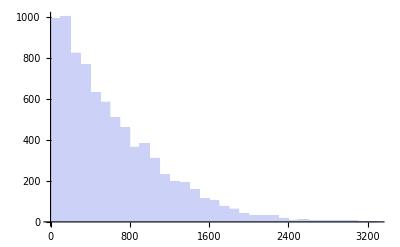

```mathematica
hot=data[[All,posTurnOut]];
zeroSizePos=Flatten[Position[hot,0]];
hot2=DeleteCases[hot,0];
hot2//Length
Stats[hot2]
Histogram[hot2]
```

### Random Choice with Weights

```mathematica
cand={"r","d","o"};
weights={.55,.44,.05};
dist=Map[DistrictVoteGenerator[cand,weights,#]&,hot2];
chiStat=Map[X2B2,Transpose[dist]];
pValue=Map[PValue,chiStat];
TableForm[Transpose[{cand,chiStat,pValue}]]
```

r | 8.55863 | 0.478972
d | 8.74422 | 0.461213
o | 9.96806 | 0.353077

{Mean:258.064,Median:201.,Min:0,Max:1379,Skewness:1.24547}

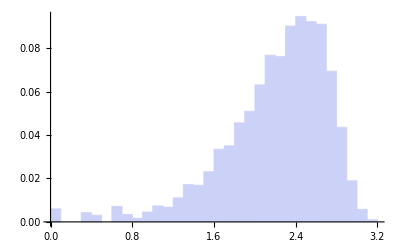

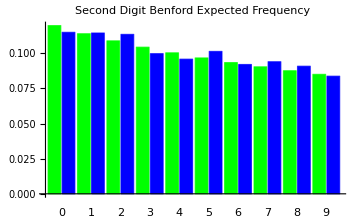
-Graphics--Graphics- | 2BL
-Graphics- | Data

```mathematica
focus=dist[[All,2]];
Stats[focus]
DataLogPlot[focus]
BLHistogram[focus]
```

### Mechanism A

```mathematica
cand={"r","d"};
mf=1/3;
lgp=1;
hgp=1;
lb=4;
ha=4;
```

```mathematica
MechA[50,mf,lgp,hgp,lb,ha]
```

{26,24}

```mathematica
dist=Map[MechA[#,mf,lgp,hgp,lb,ha]&,hot2];
chiStat=Map[X2B2,Transpose[dist]];
pValue=Map[PValue,chiStat];
TableForm[Transpose[{cand,chiStat,pValue}]]
```

{Mean:279.425,Median:193.,Min:0,Max:2263,Skewness:1.86497}

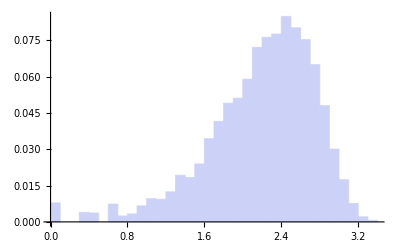

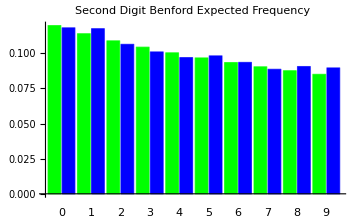
-Graphics--Graphics- | 2BL
-Graphics- | Data

```mathematica
focus=dist[[All,1]];
Stats[focus]
DataLogPlot[focus]
BLHistogram[focus]
```

## Understanding Equations

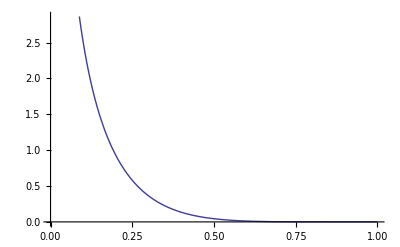

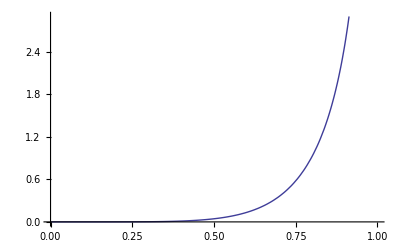

{0.0851596,0.333333,0.996368}

```mathematica
lb=6.5;
ha=6.5;
mf=N[1/3];
Plot[PDF[BetaDistribution[1/2,lb],x],{x,0,1},AxesOrigin-> {0,0}]
Plot[PDF[BetaDistribution[ha,1/2],x],{x,0,1},AxesOrigin-> {0,0}]
{RandomVariate[BetaDistribution[1/2,lb]],mf,RandomVariate[BetaDistribution[ha,1/2]]}
```

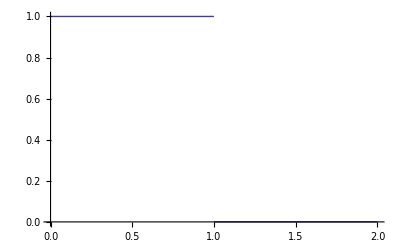

0.217527

```mathematica
Plot[PDF[UniformDistribution[{0,1}],x],{x,0,2}]
RandomVariate[UniformDistribution[{0,1}]]
```

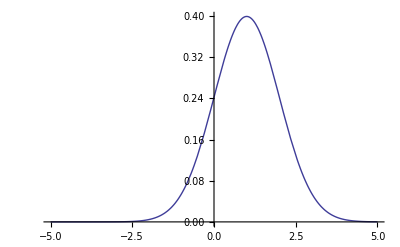

```mathematica
Plot[PDF[NormalDistribution[1,1],x],{x,-5,5},AxesOrigin-> {0,0}]
```

```mathematica
onex=RandomVariate[NormalDistribution[1,1]]
twox=RandomVariate[NormalDistribution[1,1]]
Exp[onex]
Exp[twox]
```

0.307946

-0.047729

1.36063

0.953392

```mathematica
x=3;
y=3;
N[Exp[x]]
N[Exp[y]]
oneP=N[1/(Exp[x]+Exp[y]+1)];
xP=N[Exp[x]/(Exp[x]+Exp[y]+1)];
yP=N[Exp[y]/(Exp[x]+Exp[y]+1)];
Print["oneP="<>ToString[oneP]]
Print["xP="<>ToString[xP]]
Print["yP="<>ToString[yP]]
Total[{oneP,xP,yP}]
```

20.0855

20.0855

oneP=0.0242889

xP=0.487856

yP=0.487856

1.

```mathematica
q=RandomVariate[UniformDistribution[{0,1}]]
pf={q*xP,oneP,(1-q)*yP}
Total[pf]
pfNorm=pf/Total[pf]
Total[pfNorm]
```

0.186677

{0.0910716,0.0242889,0.396784}

0.512144

{0.177824,0.0474259,0.77475}

1.

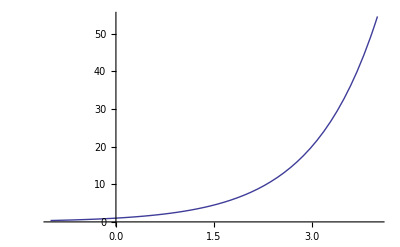

```mathematica
Plot[Exp[x],{x,-1,4}]
```

```mathematica
g=3;
h=4;
gp=g 0.5
hp=h 0.5
gp+hp
```

1.5

2.

3.5

## Policy Based Vote

### Functions

```mathematica
UniRand[]:=Module[{},
RandomVariate[UniformDistribution[{0,1}]]
]
```

```mathematica
PoliticalPlayer[numPolices_]:=Module[{},
Table[UniRand[],{x,numPolices}]
]
```

```mathematica
P[b_,x_,k_]:=Module[{},
∑_(j=1)^Length[k] b[[j]]*(x[[j]]-k[[j]])^2
];
```

```mathematica
VoterChoice[voterI_,b_,candidates_]:=Module[{scores},
scores=Map[P[b,#,voterI]&,candidates];
First[Ordering[scores,1]]
]
```

```mathematica
DistrictTally[voters_,b_,candidates_]:=Module[{},
Sort[Tally[Map[VoterChoice[#,b,candidates]&,voters]]]
]
```

```mathematica
RandomVoters[nVoters_,candidates_,nPolices_,b_]:=Module[{voter,nCandidates,tally,range,freeq,posq},
voter=Table[PoliticalPlayer[nPolices],{x,nVoters}];
nCandidates=Length[candidates];
tally=DistrictTally[voter,b,candidates];
If[Length[tally]== nCandidates,tally[[All,2]],
range=Range[nCandidates];
freeq=Map[FreeQ[tally[[All,1]],#]&,range];
posq=Flatten[Position[freeq,True]];
Sort[Join[tally,Map[{#,0}&,range[[posq]]]]][[All,2]]
]
]
```

```mathematica
ElectionResults[precictVotes_]:=Module[{totalsPerCand,totalVotes},
totalsPerCand=Map[Total,Transpose[precictVotes]];
totalVotes=Total[totalsPerCand];
N[totalsPerCand/totalVotes]
]
```

```mathematica
Coord[val_,dim2_]:=Module[{mod,row,col},
mod=Mod[val,dim2];
If[mod==0,
row=val/dim2;
col=dim2;
,
row=Floor[val/dim2+1];
col=mod;
];
{row,col}
];
```

### Random Candidates and Voters

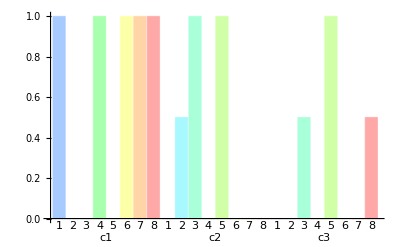

```mathematica
nCandidates=3;
cand=Range[nCandidates];
nPolices=8;
b=Table[1,{x,nPolices}];
(*candidate=Table[PoliticalPlayer[nPolices],{x,nCandidates}];*)
candidate=({{1, 0, 0, 1, 0, 1, 1, 1}, {0, .5, 1, 0, 1, 0, 0, 0}, {0, 0, .5, 0, 1, 0, 0, .5}});
(*
c1=Left wing;
c2=Right wing;
c3=Others;

1: Should abortion remain a legal option in America?;
2: Should law enforcement be allowed to use racial profiling?;
3: Should the federal deficit be reduced without raising any taxes?;
4: Are the March 2010 federal health care reform laws ("Obamacare") good for America?;
5: Should state and local law enforcement be empowered to enforce federal immigration laws?;
6: Should gay marriage be legal?;
7: Should marijuana be a medical option?;
8: Should the wealthiest 1% of Americans be taxed more heavily?;
Source->http://2012election.procon.org/view.source-summary-chart.php;
*)
BarChart[candidate,ChartLabels-> {{"c1","c2","c3"},Range[nPolices]}]
```

```mathematica
AbsoluteTiming[
dist=Map[RandomVoters[#,candidate,nPolices,b]&,hot2[[;;10]]];
][[1]]/60
```

0.009817648

```mathematica
dist=<<(nd<>"tests//p1_2.txt");
```

```mathematica
dist//Length
```

8173

#### Batch

```mathematica
PolicyBasedElection[runs_,testID_]:=Module[{dist,chiStat,pValue,adjustedPValue,electionResults,results},
results=Table[
Print[ToString[i]<>": "];
Print[ToString[AbsoluteTiming[
dist=Map[RandomVoters[#,candidate,nPolices,b]&,hot2];
][[1]]/60]];
dist>>(nd<>"tests//p"<>ToString[testID]<>"_"<>ToString[i]<>".txt");

chiStat=Map[X2B2,Transpose[dist]];
pValue=Map[PValue,chiStat];
adjustedPValue=AdjustedPValue[pValue];

electionResults=ElectionResults[dist];
Transpose[{cand,chiStat,pValue,adjustedPValue,electionResults}]
,{i,runs}];
results>>(nd<>"tests//result_"<>ToString[testID]<>".txt");
results
]
```

```mathematica
res=PolicyBasedElection[50,1];
```

```mathematica
res=<<(nd<>"tests//result_4.txt");
pval=res[[All,All,4]];
(*pval=Map[Map[PValue,#]&,pval];*)
pvalBool=Table[Map[Boole[#>0.05]&,Transpose[pval][[i]]],{i,Dimensions[pval][[2]]}];
Map[Tally,pvalBool]
```

{{{1,44},{0,6}},{{1,50}},{{1,50}}}

```mathematica
(*Calculating average false discovery from adjusted pvalue*)
m={{{{1,42},{0,8}},{{1,49},{0,1}},{{1,50}}},{{{1,42},{0,8}},{{1,49},{0,1}},{{1,50}}},{{{1,45},{0,5}},{{1,49},{0,1}},{{1,50}}},{{{1,44},{0,6}},{{1,50}},{{1,50}}}};
N[Mean[Cases[Flatten[m,2],{0,_}][[All,2]]]/50]
```

0.0857143

```mathematica
(*Calculating average false discovery*)
m={{{{1,49},{0,1}},{{1,47},{0,3}},{{0,8},{1,42}}},{{{1,46},{0,4}},{{1,49},{0,1}},{{1,44},{0,6}}},{{{1,46},{0,4}},{{1,49},{0,1}},{{1,45},{0,5}}},{{{1,48},{0,2}},{{1,47},{0,3}},{{1,41},{0,9}}}};
N[Mean[Cases[Flatten[m,2],{0,_}][[All,2]]]/50]
```

0.0783333

#### Filtering Small Precincts

```mathematica
filtering=Table[
bool=Map[Boole[#>x]&,hot2];
distSub=Pick[dist,bool,1];
chiStat=Map[X2B2,Transpose[distSub]];
{x,AdjustedPValue[Map[PValue,chiStat]]}
,{x,10,120,10}];
```

```mathematica
th=Plot[0.05,{x,0,42},PlotStyle->Red];
bar=BarChart[filtering[[All,2]],ChartLabels->{filtering[[All,1]],Range[nCandidates]}];
Show[bar,th]
```

#### Not Filtering

```mathematica
dist=<<(nd<>"tests//p2_40.txt");

bool=Map[Boole[#>0]&,hot2];
distSub=Pick[dist,bool,1];
chiStat=Map[X2B2,Transpose[distSub]];
pValue=Map[PValue,chiStat];
adjustedPValue=AdjustedPValue[pValue];
electionResults=ElectionResults[distSub];
TableForm[Transpose[{cand,chiStat,pValue,adjustedPValue,electionResults}]]

ControlledFDR[{pValue},True]
```

1 | 3.01858 | 0.963554 | 0.173629 | 0.339798
2 | 16.4599 | 0.0578762 | 0.963554 | 0.255482
3 | 6.34872 | 0.704572 | 0.963554 | 0.40472

d = 0

d | PValue | ID | St | Decision
1 | 0.0578762 | 2 | 0.0166667 | Accepted
2 | 0.704572 | 3 | 0.0333333 | Accepted
3 | 0.963554 | 1 | 0.05 | Accepted

{}

{Mean:207.361,Median:163.,Min:0,Max:1089,Skewness:1.25298}

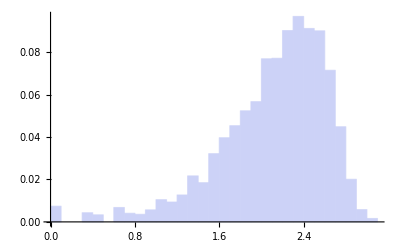

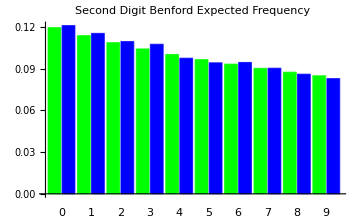
-Graphics--Graphics- | 2BL
-Graphics- | Data

```mathematica
focus=dist[[All,1]];
Stats[focus]
DataLogPlot[focus]
BLHistogram[focus]
```

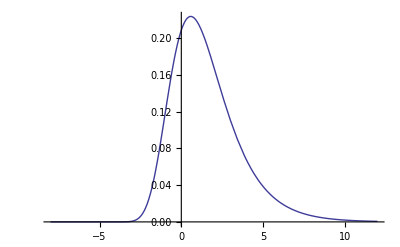

```mathematica
Plot[PDF[ExtremeValueDistribution[EulerGamma,Pi^2/6],x],{x,-8,12}]
```